```mathematica
SetToSets[s_]:=Map[{#}&,s]
```

```mathematica
Clear[RepType];RepType[base_]:=RepType[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->SetsToSymbol2[SetToSets[PartitionType[SymbolToSets[allGraphs5[key,Bases[base,"Colofour"]]]]],base],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
RepType["C"]
```

{v1x2x3x4x5→C1x1x1x1x1,v12x3x4x5→C2x1x1x1,v13x2x4x5→C2x1x1x1,v14x2x3x5→C2x1x1x1,v15x2x3x4→C2x1x1x1,v1x23x4x5→C2x1x1x1,v1x24x3x5→C2x1x1x1,v1x25x3x4→C2x1x1x1,v1x2x34x5→C2x1x1x1,v1x2x35x4→C2x1x1x1,v1x2x3x45→C2x1x1x1,v123x4x5→C3x1x1,v124x3x5→C3x1x1,v125x3x4→C3x1x1,v12x34x5→C2x2x1,v12x35x4→C2x2x1,v12x3x45→C2x2x1,v134x2x5→C3x1x1,v135x2x4→C3x1x1,v13x24x5→C2x2x1,v13x25x4→C2x2x1,v13x2x45→C2x2x1,v145x2x3→C3x1x1,v14x23x5→C2x2x1,v14x25x3→C2x2x1,v14x2x35→C2x2x1,v15x23x4→C2x2x1,v15x24x3→C2x2x1,v15x2x34→C2x2x1,v1x234x5→C3x1x1,v1x235x4→C3x1x1,v1x23x45→C2x2x1,v1x245x3→C3x1x1,v1x24x35→C2x2x1,v1x25x34→C2x2x1,v1x2x345→C3x1x1,v1234x5→C4x1,v1235x4→C4x1,v123x45→C3x2,v1245x3→C4x1,v124x35→C3x2,v125x34→C3x2,v12x345→C3x2,v1345x2→C4x1,v134x25→C3x2,v135x24→C3x2,v13x245→C3x2,v145x23→C3x2,v14x235→C3x2,v15x234→C3x2,v1x2345→C4x1,v12345→C5}

```mathematica
varsC=ReverseSort[DeleteDuplicates[Table[allGraphs5[k,"colofour"]/.RepType["C"],{k,allGraphs5AtomKeys}]],CompareSymbols]
```

{C5,C4x1,C3x2,C3x1x1,C2x2x1,C2x1x1x1,C1x1x1x1x1}

```mathematica
varsC={C5,C3x2,C4x1,C3x1x1,C2x2x1,C2x1x1x1,C1x1x1x1x1}
```

{C5,C3x2,C4x1,C3x1x1,C2x2x1,C2x1x1x1,C1x1x1x1x1}

```mathematica
BaseCoeffC[key_]:=With[{form=allGraphs5[key,"colofour"]/.RepType["C"]},
Table[Coefficient[form,var],{var,varsC}]
]
```

```mathematica
allGraphs6//Length
```

0

```mathematica
DeleteDuplicates[Table[Reverse[BaseCoeffC[k]],{k,allGraphs5NullAtomKeys}]]//Sort//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 2 | 1 | 1
0 | 0 | 1 | 0 | 1 | 2 | 1
0 | 1 | 3 | 3 | 3 | 4 | 1
1 | 10 | 15 | 10 | 5 | 10 | 1)

```mathematica
DeleteDuplicates[Table[Reverse[BaseCoeffC[k]],{k,allGraphs5NullAtomKeys}]]//Sort//Det
```

-1

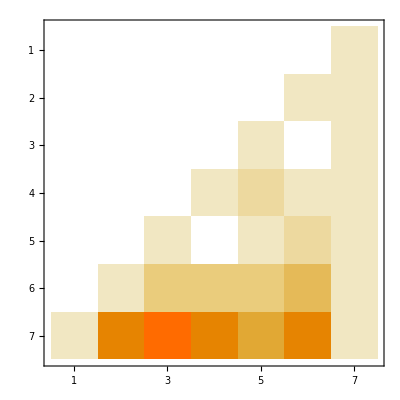

```mathematica
DeleteDuplicates[Table[Reverse[BaseCoeffC[k]],{k,allGraphs5NullAtomKeys}]]//Sort//MatrixPlot
```

```mathematica
allGraphs6=Get["d:\\saved\\allGraphs6-fullfullgen.m"];
```

```mathematica
Clear[RepType6];RepType6[base_]:=RepType6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->SetsToSymbol2[SetToSets[PartitionType[SymbolToSets[allGraphs6[key,Bases6[base,"Colofour"]]]]],base],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
RepType6["C"]
```

{v1x2x3x4x5x6→C1x1x1x1x1x1,v12x3x4x5x6→C2x1x1x1x1,v13x2x4x5x6→C2x1x1x1x1,v14x2x3x5x6→C2x1x1x1x1,v15x2x3x4x6→C2x1x1x1x1,v16x2x3x4x5→C2x1x1x1x1,v1x23x4x5x6→C2x1x1x1x1,v1x24x3x5x6→C2x1x1x1x1,v1x25x3x4x6→C2x1x1x1x1,v1x26x3x4x5→C2x1x1x1x1,v1x2x34x5x6→C2x1x1x1x1,v1x2x35x4x6→C2x1x1x1x1,v1x2x36x4x5→C2x1x1x1x1,v1x2x3x45x6→C2x1x1x1x1,v1x2x3x46x5→C2x1x1x1x1,v1x2x3x4x56→C2x1x1x1x1,v123x4x5x6→C3x1x1x1,v124x3x5x6→C3x1x1x1,v125x3x4x6→C3x1x1x1,v126x3x4x5→C3x1x1x1,v12x34x5x6→C2x2x1x1,v12x35x4x6→C2x2x1x1,v12x36x4x5→C2x2x1x1,v12x3x45x6→C2x2x1x1,v12x3x46x5→C2x2x1x1,v12x3x4x56→C2x2x1x1,v134x2x5x6→C3x1x1x1,v135x2x4x6→C3x1x1x1,v136x2x4x5→C3x1x1x1,v13x24x5x6→C2x2x1x1,v13x25x4x6→C2x2x1x1,v13x26x4x5→C2x2x1x1,v13x2x45x6→C2x2x1x1,v13x2x46x5→C2x2x1x1,v13x2x4x56→C2x2x1x1,v145x2x3x6→C3x1x1x1,v146x2x3x5→C3x1x1x1,v14x23x5x6→C2x2x1x1,v14x25x3x6→C2x2x1x1,v14x26x3x5→C2x2x1x1,v14x2x35x6→C2x2x1x1,v14x2x36x5→C2x2x1x1,v14x2x3x56→C2x2x1x1,v156x2x3x4→C3x1x1x1,v15x23x4x6→C2x2x1x1,v15x24x3x6→C2x2x1x1,v15x26x3x4→C2x2x1x1,v15x2x34x6→C2x2x1x1,v15x2x36x4→C2x2x1x1,v15x2x3x46→C2x2x1x1,v16x23x4x5→C2x2x1x1,v16x24x3x5→C2x2x1x1,v16x25x3x4→C2x2x1x1,v16x2x34x5→C2x2x1x1,v16x2x35x4→C2x2x1x1,v16x2x3x45→C2x2x1x1,v1x234x5x6→C3x1x1x1,v1x235x4x6→C3x1x1x1,v1x236x4x5→C3x1x1x1,v1x23x45x6→C2x2x1x1,v1x23x46x5→C2x2x1x1,v1x23x4x56→C2x2x1x1,v1x245x3x6→C3x1x1x1,v1x246x3x5→C3x1x1x1,v1x24x35x6→C2x2x1x1,v1x24x36x5→C2x2x1x1,v1x24x3x56→C2x2x1x1,v1x256x3x4→C3x1x1x1,v1x25x34x6→C2x2x1x1,v1x25x36x4→C2x2x1x1,v1x25x3x46→C2x2x1x1,v1x26x34x5→C2x2x1x1,v1x26x35x4→C2x2x1x1,v1x26x3x45→C2x2x1x1,v1x2x345x6→C3x1x1x1,v1x2x346x5→C3x1x1x1,v1x2x34x56→C2x2x1x1,v1x2x356x4→C3x1x1x1,v1x2x35x46→C2x2x1x1,v1x2x36x45→C2x2x1x1,v1x2x3x456→C3x1x1x1,v1234x5x6→C4x1x1,v1235x4x6→C4x1x1,v1236x4x5→C4x1x1,v123x45x6→C3x2x1,v123x46x5→C3x2x1,v123x4x56→C3x2x1,v1245x3x6→C4x1x1,v1246x3x5→C4x1x1,v124x35x6→C3x2x1,v124x36x5→C3x2x1,v124x3x56→C3x2x1,v1256x3x4→C4x1x1,v125x34x6→C3x2x1,v125x36x4→C3x2x1,v125x3x46→C3x2x1,v126x34x5→C3x2x1,v126x35x4→C3x2x1,v126x3x45→C3x2x1,v12x345x6→C3x2x1,v12x346x5→C3x2x1,v12x34x56→C2x2x2,v12x356x4→C3x2x1,v12x35x46→C2x2x2,v12x36x45→C2x2x2,v12x3x456→C3x2x1,v1345x2x6→C4x1x1,v1346x2x5→C4x1x1,v134x25x6→C3x2x1,v134x26x5→C3x2x1,v134x2x56→C3x2x1,v1356x2x4→C4x1x1,v135x24x6→C3x2x1,v135x26x4→C3x2x1,v135x2x46→C3x2x1,v136x24x5→C3x2x1,v136x25x4→C3x2x1,v136x2x45→C3x2x1,v13x245x6→C3x2x1,v13x246x5→C3x2x1,v13x24x56→C2x2x2,v13x256x4→C3x2x1,v13x25x46→C2x2x2,v13x26x45→C2x2x2,v13x2x456→C3x2x1,v1456x2x3→C4x1x1,v145x23x6→C3x2x1,v145x26x3→C3x2x1,v145x2x36→C3x2x1,v146x23x5→C3x2x1,v146x25x3→C3x2x1,v146x2x35→C3x2x1,v14x235x6→C3x2x1,v14x236x5→C3x2x1,v14x23x56→C2x2x2,v14x256x3→C3x2x1,v14x25x36→C2x2x2,v14x26x35→C2x2x2,v14x2x356→C3x2x1,v156x23x4→C3x2x1,v156x24x3→C3x2x1,v156x2x34→C3x2x1,v15x234x6→C3x2x1,v15x236x4→C3x2x1,v15x23x46→C2x2x2,v15x246x3→C3x2x1,v15x24x36→C2x2x2,v15x26x34→C2x2x2,v15x2x346→C3x2x1,v16x234x5→C3x2x1,v16x235x4→C3x2x1,v16x23x45→C2x2x2,v16x245x3→C3x2x1,v16x24x35→C2x2x2,v16x25x34→C2x2x2,v16x2x345→C3x2x1,v1x2345x6→C4x1x1,v1x2346x5→C4x1x1,v1x234x56→C3x2x1,v1x2356x4→C4x1x1,v1x235x46→C3x2x1,v1x236x45→C3x2x1,v1x23x456→C3x2x1,v1x2456x3→C4x1x1,v1x245x36→C3x2x1,v1x246x35→C3x2x1,v1x24x356→C3x2x1,v1x256x34→C3x2x1,v1x25x346→C3x2x1,v1x26x345→C3x2x1,v1x2x3456→C4x1x1,v12345x6→C5x1,v12346x5→C5x1,v1234x56→C4x2,v12356x4→C5x1,v1235x46→C4x2,v1236x45→C4x2,v123x456→C3x3,v12456x3→C5x1,v1245x36→C4x2,v1246x35→C4x2,v124x356→C3x3,v1256x34→C4x2,v125x346→C3x3,v126x345→C3x3,v12x3456→C4x2,v13456x2→C5x1,v1345x26→C4x2,v1346x25→C4x2,v134x256→C3x3,v1356x24→C4x2,v135x246→C3x3,v136x245→C3x3,v13x2456→C4x2,v1456x23→C4x2,v145x236→C3x3,v146x235→C3x3,v14x2356→C4x2,v156x234→C3x3,v15x2346→C4x2,v16x2345→C4x2,v1x23456→C5x1,v123456→C6}

```mathematica
varsC6=ReverseSort[DeleteDuplicates[Table[allGraphs6[k,"colofour"]/.RepType6["C"],{k,allGraphs6AtomKeys}]],CompareSymbols]
```

{C6,C5x1,C4x2,C3x3,C4x1x1,C3x2x1,C2x2x2,C3x1x1x1,C2x2x1x1,C2x1x1x1x1,C1x1x1x1x1x1}

```mathematica
BaseCoeffC6[key_]:=With[{form=allGraphs6[key,"colofour"]/.RepType6["C"]},
Table[Coefficient[form,var],{var,varsC6}]
]
```

```mathematica
DeleteDuplicates[Table[Reverse[BaseCoeffC6[k]],{k,allGraphs6NullAtomKeys}]]//Sort//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 2 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 0 | 1
0 | 0 | 0 | 1 | 0 | 3 | 3 | 1 | 3 | 3 | 1
0 | 0 | 1 | 0 | 1 | 4 | 1 | 2 | 3 | 2 | 1
0 | 1 | 6 | 4 | 3 | 16 | 6 | 4 | 7 | 4 | 1
1 | 15 | 45 | 20 | 15 | 60 | 15 | 10 | 15 | 6 | 1)

```mathematica
allGraphs6[0,"colofour"]/.RepType6["C"]
```

C1x1x1x1x1x1+15 C2x1x1x1x1+45 C2x2x1x1+15 C2x2x2+20 C3x1x1x1+60 C3x2x1+10 C3x3+15 C4x1x1+15 C4x2+6 C5x1+C6

```mathematica
K6Key
```

First[Keys[]]

```mathematica
allGraphs6[K6Key,"colofourgenerator"]
```

Missing[KeyAbsent,First[Keys[]]]

```mathematica
allGraphs6[K6Key,"colofourgenerator"]/.RepType6["G"]
```

Missing[KeyAbsent,First[Keys[]]]

```mathematica
allGraphs6[0,"colofourgenerator"]/.RepType6["G"]
```

G6

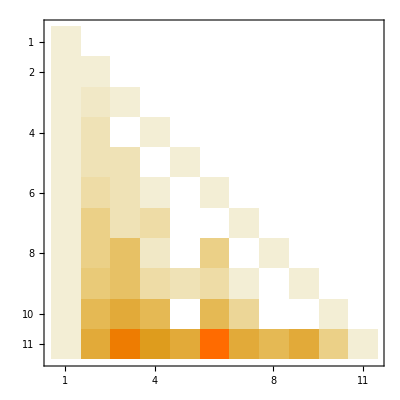

```mathematica
DeleteDuplicates[Table[Reverse[BaseCoeffC6[k]],{k,allGraphs6GeneratorAtomKeys}]]//Sort//MatrixPlot
```

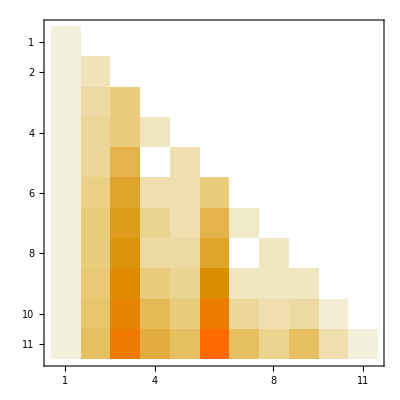

```mathematica
DeleteDuplicates[Table[Reverse[BaseCoeffC6[k]],{k,allGraphs6FakeAtomKeys}]]//Sort//MatrixPlot
```

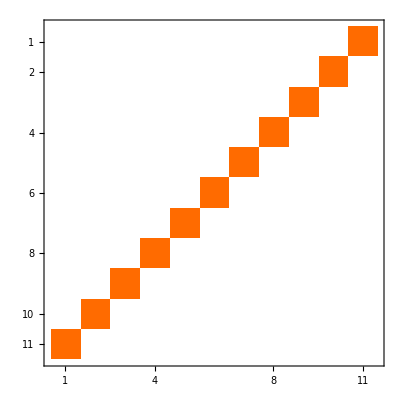

```mathematica
DeleteDuplicates[Table[Reverse[BaseCoeffC6[k]],{k,allGraphs6AtomKeys}]]//Sort//MatrixPlot
```

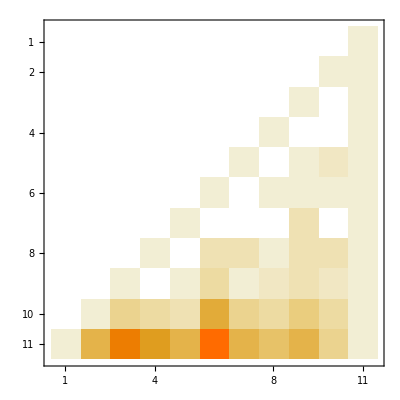

```mathematica
DeleteDuplicates[Table[Reverse[BaseCoeffC6[k]],{k,allGraphs6NullAtomKeys}]]//Sort//MatrixPlot
```

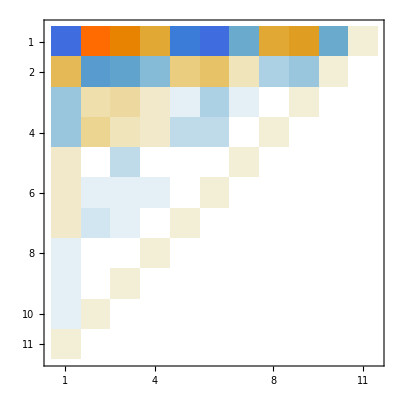

```mathematica
DeleteDuplicates[Table[Reverse[BaseCoeffC6[k]],{k,allGraphs6NullAtomKeys}]]//Sort//Inverse//MatrixPlot
```

```mathematica
(DeleteDuplicates[Table[Reverse[BaseCoeffC6[k]],{k,allGraphs6NullAtomKeys}]]//Sort//Inverse)+(DeleteDuplicates[Table[Reverse[BaseCoeffC6[k]],{k,allGraphs6NullAtomKeys}]]//Sort)-IdentityMatrix[PartitionsP[6]]//Inverse//MatrixForm
```

(14/1251 | 373/7506 | -110/3753 | -107/1251 | 1927/7506 | -221/1251 | 269/3753 | -448/3753 | 455/3753 | -416/3753 | 25/834
-835/15012 | -899/2502 | -511/5004 | 1369/7506 | 317/7506 | 126/139 | -62/3753 | -1153/7506 | -2302/3753 | 3379/15012 | -59/3753
323/7506 | 4103/15012 | 2731/3753 | -4921/7506 | 8965/15012 | -1597/2502 | -3157/7506 | -2186/3753 | 811/1251 | -89/2502 | 251/15012
53/5004 | 79/1668 | -795/556 | 1460/1251 | -4829/5004 | -175/278 | 2819/2502 | 3563/2502 | -175/1251 | -3113/5004 | 415/5004
11/1668 | 671/11259 | -2009/45036 | 133/7506 | 8456/11259 | -5561/3753 | 4931/11259 | -11453/22518 | 10100/11259 | -6377/45036 | 145/7506
-121/2502 | -2153/7506 | -1591/7506 | 42/139 | -5741/7506 | 1933/1251 | -532/3753 | 1658/3753 | -3808/3753 | 1709/7506 | -61/2502
1411/15012 | 14231/22518 | 57659/45036 | -8177/7506 | 41189/22518 | -9448/3753 | -5963/11259 | -33001/22518 | 17980/11259 | 3407/45036 | -4/1251
265/5004 | 2125/7506 | -14195/15012 | 155/278 | 409/7506 | -2339/1251 | 3281/3753 | 2293/7506 | 4325/3753 | -7775/15012 | 67/1251
-199/15012 | -1855/15012 | 5737/15012 | -1603/3753 | 103/1668 | 1667/2502 | -673/2502 | -227/834 | -1205/3753 | 4943/15012 | -677/15012
-343/7506 | -583/1668 | -970/1251 | 2969/7506 | -7513/15012 | 563/834 | 2089/7506 | 2756/3753 | -410/3753 | -1931/7506 | 317/15012
25/834 | 2543/7506 | 6043/7506 | 46/1251 | 2327/7506 | -31/1251 | -734/3753 | -1061/3753 | -206/3753 | 55/7506 | 47/2502)

```mathematica
FactorInteger[21335850]
```

{{2,1},{3,2},{5,2},{17,1},{2789,1}}

```mathematica
DeleteDuplicates[Table[Reverse[BaseCoeffC[k]],{k,allGraphs5NullAtomKeys}]]//Sort//Inverse//MatrixForm
```

(24 | -20 | -30 | 20 | 15 | -10 | 1
-6 | 5 | 6 | -3 | -3 | 1 | 0
2 | -2 | -1 | 0 | 1 | 0 | 0
2 | -1 | -2 | 1 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
DeleteDuplicates[Table[Reverse[BaseCoeffC[k]],{k,allGraphs5NullAtomKeys}]]//Sort//Inverse//Det
```

-1

```mathematica
BaseCoeffC[1]
```

{0,6,2,7,12,9,1}

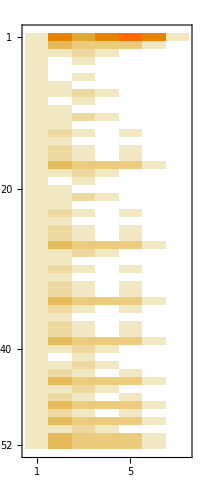

```mathematica
Table[BaseCoeffC[k],{k,allGraphs5NullAtomKeys}]//MatrixPlot
```

```mathematica
DeleteDuplicates[Table[BaseCoeffC[k],{k,allGraphs5NullAtomKeys}]]//Sort//Inverse//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | 0
2 | -2 | -1 | 1 | 0 | 0 | 0
2 | -1 | -2 | 0 | 1 | 0 | 0
-6 | 6 | 5 | -3 | -3 | 1 | 0
24 | -30 | -20 | 20 | 15 | -10 | 1)

```mathematica
Table[allGraphs5[k,"colofour"]/.RepType["C"],{k,allGraphs5NullAtomKeys}]//TableForm
```

C1x1x1x1x1+10 C2x1x1x1+15 C2x2x1+10 C3x1x1+10 C3x2+5 C4x1+C5
C2x1x1x1+3 C2x2x1+3 C3x1x1+4 C3x2+3 C4x1+C5
C3x1x1+C3x2+2 C4x1+C5
C4x1+C5
C5
C4x1+C5
C3x2+C5
C3x1x1+C3x2+2 C4x1+C5
C4x1+C5
C3x2+C5
C3x1x1+C3x2+2 C4x1+C5
C3x2+C5
C2x2x1+2 C3x2+C4x1+C5
C3x2+C5
C2x2x1+2 C3x2+C4x1+C5
C2x2x1+2 C3x2+C4x1+C5
C2x1x1x1+3 C2x2x1+3 C3x1x1+4 C3x2+3 C4x1+C5
C3x1x1+C3x2+2 C4x1+C5
C4x1+C5
C3x2+C5
C3x1x1+C3x2+2 C4x1+C5
C3x2+C5
C2x2x1+2 C3x2+C4x1+C5
C3x2+C5
C2x2x1+2 C3x2+C4x1+C5
C2x2x1+2 C3x2+C4x1+C5
C2x1x1x1+3 C2x2x1+3 C3x1x1+4 C3x2+3 C4x1+C5
C3x1x1+C3x2+2 C4x1+C5
C3x2+C5
C2x2x1+2 C3x2+C4x1+C5
C3x2+C5
C2x2x1+2 C3x2+C4x1+C5
C2x2x1+2 C3x2+C4x1+C5
C2x1x1x1+3 C2x2x1+3 C3x1x1+4 C3x2+3 C4x1+C5
C2x2x1+2 C3x2+C4x1+C5
C3x2+C5
C2x2x1+2 C3x2+C4x1+C5
C2x2x1+2 C3x2+C4x1+C5
C2x1x1x1+3 C2x2x1+3 C3x1x1+4 C3x2+3 C4x1+C5
C3x1x1+C3x2+2 C4x1+C5
C4x1+C5
C3x1x1+C3x2+2 C4x1+C5
C2x2x1+2 C3x2+C4x1+C5
C2x1x1x1+3 C2x2x1+3 C3x1x1+4 C3x2+3 C4x1+C5
C3x1x1+C3x2+2 C4x1+C5
C2x2x1+2 C3x2+C4x1+C5
C2x1x1x1+3 C2x2x1+3 C3x1x1+4 C3x2+3 C4x1+C5
C2x2x1+2 C3x2+C4x1+C5
C2x1x1x1+3 C2x2x1+3 C3x1x1+4 C3x2+3 C4x1+C5
C3x1x1+C3x2+2 C4x1+C5
C2x1x1x1+3 C2x2x1+3 C3x1x1+4 C3x2+3 C4x1+C5
C2x1x1x1+3 C2x2x1+3 C3x1x1+4 C3x2+3 C4x1+C5